## Wuschel-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

This is a Cellzilla2D example that is based on the "Activator" model in 
H Jonsson, M Heisler, GV Reddy, V Agrawal, V Gor, BE Shapiro, E Mjolsness & EM Meyerowitz (2005) "Modeling the organization of the WUSCHEL expression domain in the shoot apical meristem," Bioinformatics, Vol. 21 Suppl. 1, 2005, pages i232-i240.

For more details on the model see
http://bioinformatics.oxfordjournals.org/cgi/content/abstract/21/suppl_1/i232

This CPU times shown reflect a 2015 MacBook.

```mathematica
<<xlr8r.m;
<<Cellzilla2D.m
```

xCellerator 0.95 (28-Feb-2014) loaded Fri 16 Jun 2017 10:24:20
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

Cellzilla2D (3.0.51h (15 June 2017)) loaded Fri 16 Jun 2017 10:24:20
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

## build a honeycomb template

```mathematica
ST = TemplateCircularHoneycombCover[8];
X=Centroid[ST];
XC=Mean/@Transpose[X];
```

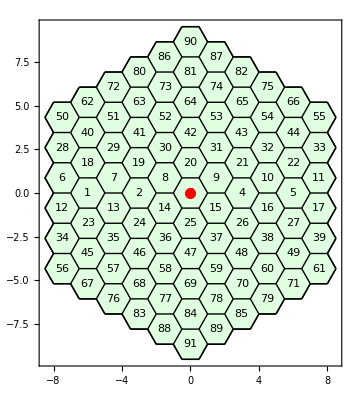

```mathematica
Show[ShowTissue[ST, Frame-> True, "CellNumbers"->True], Graphics[{Red, PointSize[.02], Point[XC]}]]
```

### DISPLAY THE CELLS ON THE BOUNDARY

```mathematica
cb=CellsOnBoundary[ST];
cb
```

{6,11,12,17,28,33,34,39,50,55,56,61,62,66,67,71,72,75,76,79,80,82,83,85,86,87,88,89,90,91}

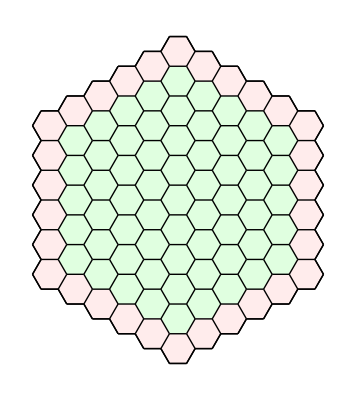

```mathematica
ShowTissueCells[ST,cb]
```

### convert to a dynamic tissue for the simulation

```mathematica
DT=Tissue2DTissue[ST];
n=NTissueCells[DT]
```

91

```mathematica
n=NTissueCells[DT]
```

91

## Define the Cellerator network that will produce the ODES as specified in the model

```mathematica
net={
{Y↦W,GRN[1/tauw,Twy,1,hw,sigma]},
{A↦W,GRN[1/tauw,Twa,1,hw,sigma]},
{W->∅,dw},
{∅⇄L1,L1[t],1},
 {L1->Y+L1,ky},
{Y->∅,dy},
{∅⇄A,a,beta},
{A+Y->Y,d},
{2 A+B->3 A,kc},
{A->B,b}
};
```

L1 is an indicator function that must be 1 on the boundary and zero elsewhere.  Te reaction for L1 ensures that it remains equal to its initial condition, as demonstrated in the following differential equation:

```mathematica
interpret[{{∅⇄L1,L1[t],1}}]
```

{{L1'[t]==0},{L1}}

Define the initial conditions of all variables. Here we use random values for A, B, W, Y.
We set L1 equal to 1 on the boundary and zero elsewhere.

```mathematica
rr:= RandomReal[]
```

```mathematica
L1IC=Table[L1[i]-> If[MemberQ[cb,i], 1,0], {i,1,n}];
```

```mathematica
ic[i_]:={A[i]->rr,B[i]->rr,W[i]->rr,Y[i]->rr};
myic=Join[Flatten[ic/@Range[n]], L1IC];
```

Define the parameters for the model

```mathematica
parameters={d-> .5,DY-> 2,  Twy->-20,Twa->0.5, ky->0.2, kz->0.2,dy->.2,dz->0.1,DZ->0.1,kD->3.0,tauw->10,dw->0.1,hw->0,a->0.1,b->0.2,beta->0.1,kc->0.1,DA->1.5,DB->15.0
};
```

## Run a StaticSimulation

```mathematica
S=StaticSimulation[DT,0,1000, 
 "tip"->False,
"xy"-> False, 
"CellVariable"-> area, 
"Internal"-> True, "Save"-> False, 
"Diffusion"-> {
{A, DA*If[MemberQ[{#1,#2},0] ,0,1]&}, 
{B, DB*If[MemberQ[{#1,#2},0] ,0,1]&},
 {Y, DY*If[MemberQ[{#1,#2},0] ,1,1]&}}, 
"Parameters"->parameters,
"Reactions"->net,
"IC"->myic,
"TestCase"->"Wuschel",
"BoundaryConditions"->{ Y-> 1},
"Verbose"->True];
```

91 Cells.

12 internal reactions in each cell.

1092 total intracellular reactions.

0 transport reactions.

1638 diffusion reactions.

0 algebraic equations for spring growth.

2730 total reactions.

Simulation Completed at t = 1000. after 0 cell divisions; Normal Exit. CPU: 120.8

Plot the results of a single variable (depending upon geometry and parameter values it can go to either a steady state or it might oscillate)

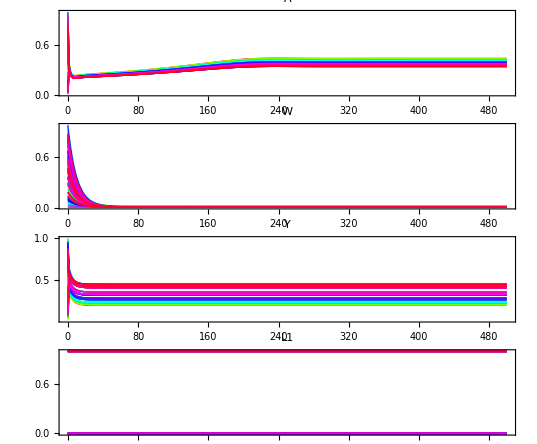

```mathematica
GraphicsColumn[SimPlot[S,{A,W,Y, L1},{0,500},AspectRatio->.2,ImageSize->500,"Points"->300]]
```

### Use SimShowFinal to find the solution at the stop time of the simulation and automatically set the scales.

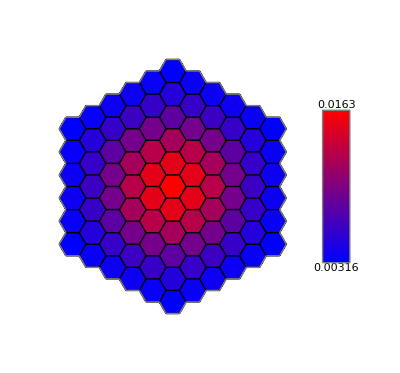

```mathematica
SimShowFinal[S,W,ST,{Blue,Red}]
```

## Use SimAnimate and ListAnimate to plot convergence

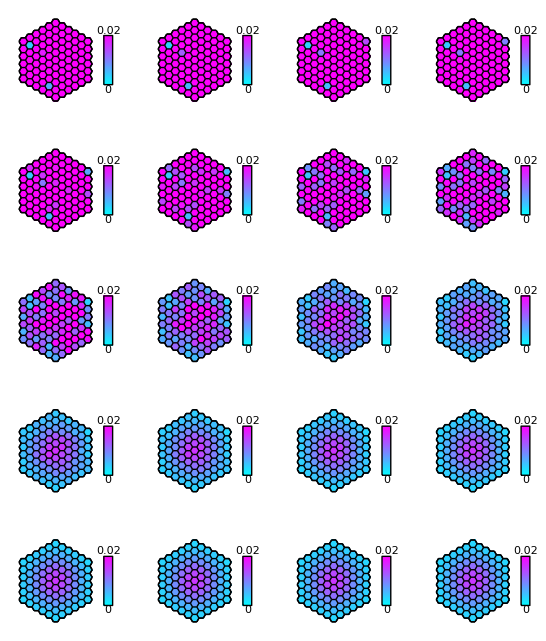

```mathematica
anim=SimAnimate[S,W,ST,{0,100,5},{Cyan,Magenta},{0,.02}];
GraphicsGrid[Partition[anim,4]]
```

```mathematica
simulation=ListAnimate[anim]
```